```mathematica
<<Combinatorica`
<<GraphUtilities`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

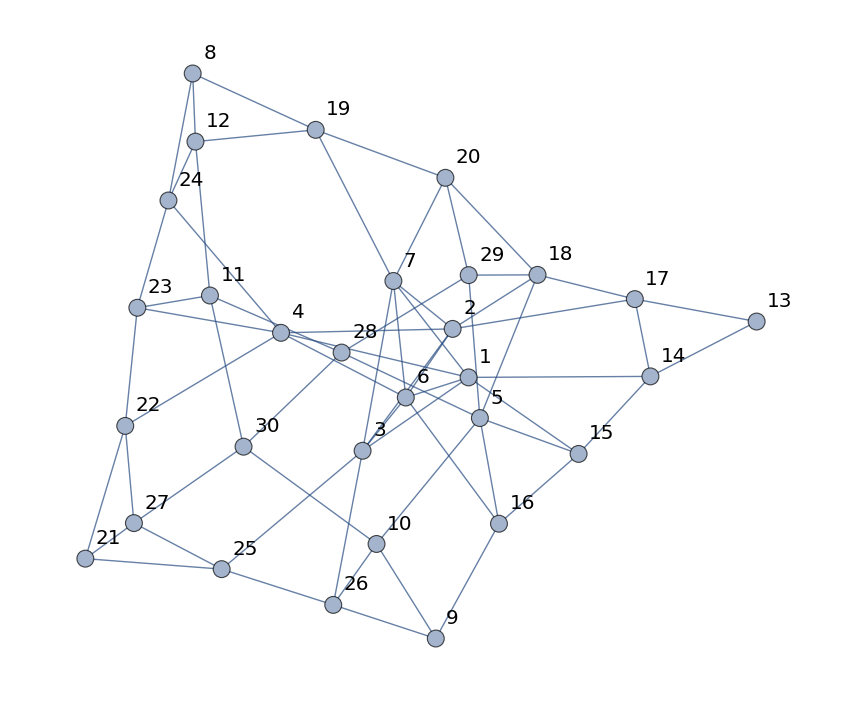

{1,2,2,2,3,3,4,1,3,1,3,3,1,2,1,1,4,3,1,1,1,3,2,1,2,3,2,2,2,1}

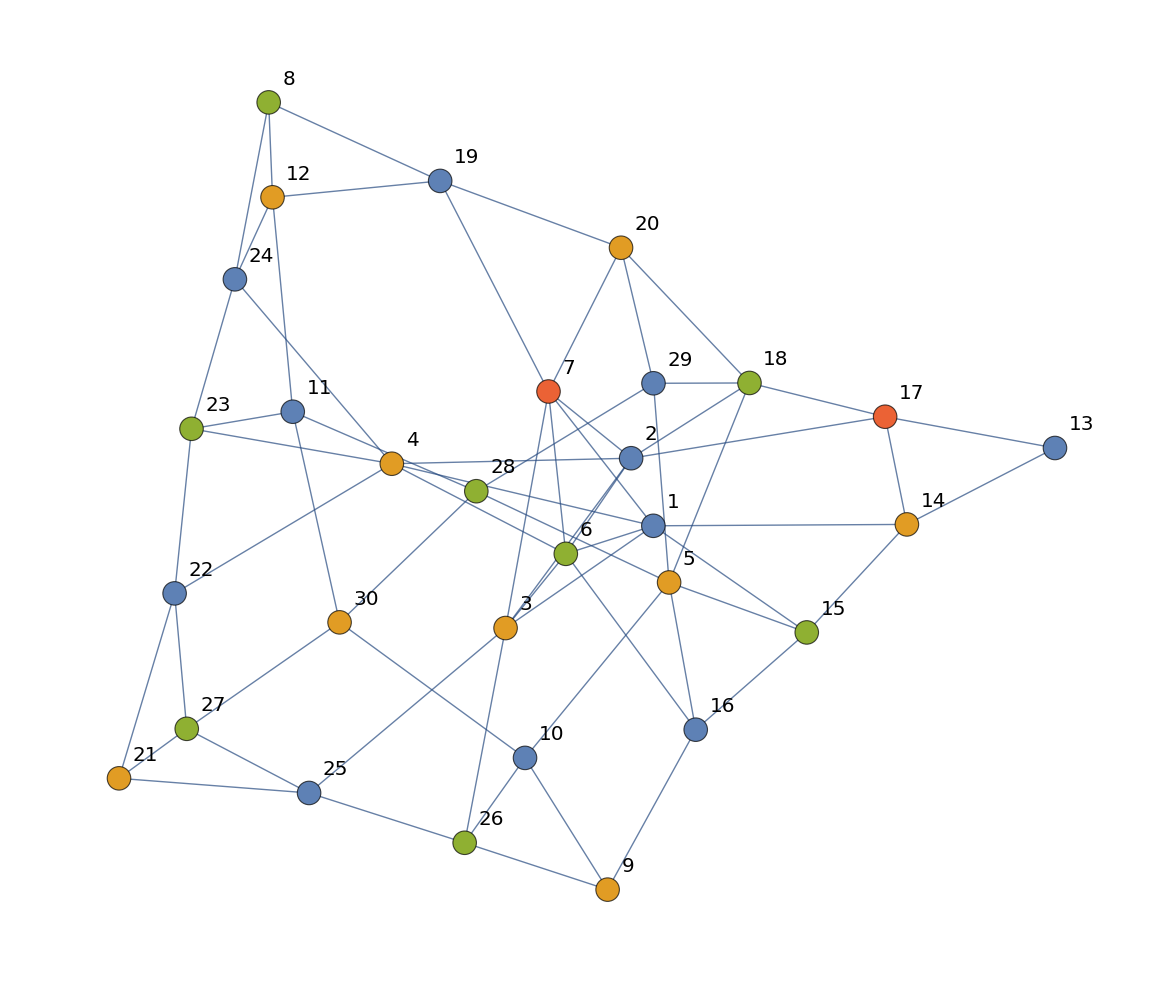

4

{1,14,3,4,15,6,7,2,18,25,26,23,24,5,16,29,17,27,22,10,11,28,12,19,20,8,9,21,30,13}

```mathematica
g=System`Graph[{1<->14,1<->3,1<->4,1<->15,1<->6,1<->7,2<->3,2<->4,2<->18,2<->6,2<->7,3<->25,3<->26,3<->6,3<->7,4<->23,4<->6,4<->24,5<->16,5<->29,6<->7,14<->17,17<->2,15<->5,18<->5,25<->27,27<->22,22<->4,26<->10,10<->5,23<->11,11<->28,28<->5,24<->12,12<->19,19<->7,16<->6,29<->20,20<->7,8<->12,9<->16,8<->19,21<->22,21<->25,21<->27,12<->11,11<->30,30<->10,10<->9,16<->15,15<->14,14<->13,19<->20,20<->18,18<->17,17<->13,22<->23,23<->24,24<->8,25<->26,26<->9,27<->30,30<->28,28<->29,29<->18},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]


GColoredList=MinimumVertexColoring@ToCombinatoricaGraph[g]
GColored=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@GColoredList)]]
Max[GColoredList]
VertexList[GColored]
```